# Plot3D and ContourPlot Assignment

### Instructions

The purpose of this assignment is to assess your knowledge of the relationship between the plot of a function of two variables and its contour plot. Please refer to the “Plot3D and ContourPlot.nb” file if you have problems with any of the questions. Some things to remember as you complete this assignment:
1.  Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF. (Make sure you Rasterize all 3-dimensional plots)
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

### Question 1 Defining a function of two variables

Define a function of two variables to be -1*(sin(y*π/3.5)+cos(x*π/3.5)). Use your first name to be the name of the function. Don’t forget to properly format your trig functions.

```mathematica
caleb[x_,y_]=-1 (Sin[y π/3.5]+Cos[x π/3.5])
```

-Cos[0.897598 x]-Sin[0.897598 y]

### Question 2 Contour Plot

a) Plot the contour plot for the function in question 1. Use x and y values that go from -4 to 4.

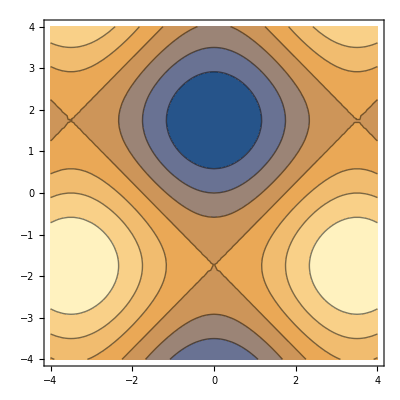

```mathematica
ContourPlot[caleb[x,y],{x,-4,4},{y,-4,4}]
```

b) The point on the graph corresponding to (0, 1.75) is best described as which of the following:
	i. bottom of a bowl		ii. hilltop	  iii. bottom of a valley	 iv. side of a hill
Create a text cell right below this cell, and type your answer.

Bottom of a bowl

c) If a ball were dropped at the point on the graph corresponding to  (0,0), which best describes the direction the ball will roll:
	i. the positive y direction 	ii. the positive x direction	iii. the negative y direction	iv. the negative x direction
Create a text cell right below this cell, and type your answer.

Positive y direction

### Question 3 Plot3D

a) Use the Plot3D command to plot the function from question 1.  Use the same range of x and y values. Note that you should be able to use this plot to confirm your answers to question 2.  Don’t forget to use the Rasterize command on this plot before saving this notebook as a pdf.

```mathematica
Rasterize[Plot3D[caleb[x,y],{x,-4,4},{y,-4,4},AxesLabel->Automatic]]
```

-Graphics-

b) Give one approximate value of (x, y) which corresponds to the highest point on the graph, just use your eyeball to find the answer, x and y should both belongs to [-4,4].

(-4,-2)

c) Is the answer from part b unique?

No, the function is periodic and there are other humps that have the same height such as (3.5,-2)